```mathematica
Clear[x];
i=5;j=7;
Array[x,{i,j,2}]
```

{{{x[1,1,1],x[1,1,2]},{x[1,2,1],x[1,2,2]},{x[1,3,1],x[1,3,2]},{x[1,4,1],x[1,4,2]},{x[1,5,1],x[1,5,2]},{x[1,6,1],x[1,6,2]},{x[1,7,1],x[1,7,2]}},{{x[2,1,1],x[2,1,2]},{x[2,2,1],x[2,2,2]},{x[2,3,1],x[2,3,2]},{x[2,4,1],x[2,4,2]},{x[2,5,1],x[2,5,2]},{x[2,6,1],x[2,6,2]},{x[2,7,1],x[2,7,2]}},{{x[3,1,1],x[3,1,2]},{x[3,2,1],x[3,2,2]},{x[3,3,1],x[3,3,2]},{x[3,4,1],x[3,4,2]},{x[3,5,1],x[3,5,2]},{x[3,6,1],x[3,6,2]},{x[3,7,1],x[3,7,2]}},{{x[4,1,1],x[4,1,2]},{x[4,2,1],x[4,2,2]},{x[4,3,1],x[4,3,2]},{x[4,4,1],x[4,4,2]},{x[4,5,1],x[4,5,2]},{x[4,6,1],x[4,6,2]},{x[4,7,1],x[4,7,2]}},{{x[5,1,1],x[5,1,2]},{x[5,2,1],x[5,2,2]},{x[5,3,1],x[5,3,2]},{x[5,4,1],x[5,4,2]},{x[5,5,1],x[5,5,2]},{x[5,6,1],x[5,6,2]},{x[5,7,1],x[5,7,2]}}}

```mathematica
LIFE=({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
xpArray=LIFE;
```

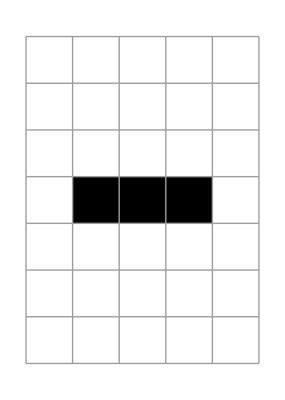

```mathematica
Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/wordLifeDirectory/IJ_1_GEN.m"]
```

```mathematica
LIFE=({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
(*AbsoluteTiming[{plt[LIFE],lifePlot[updateIJ2[LIFE] ,10]}]*)
```

```mathematica
Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/wordLifeDirectory/IJ2_1_GEN.m"]
```

ArrayPlot::mat: Argument unsatisfiable at position 1 is not a list of lists.

ArrayPlot[unsatisfiable,Frame→False,Mesh→True]

```mathematica
array3Processor[array3_]:=And@@(Or@@#&/@Flatten[array3 ,3])
```

```mathematica
Or@@{x[1,1,1],False,False,False,False,x[1,2,1],True,!x[2,1,1],!x[2,2,1],False}
```

True

```mathematica
And[]
```

True

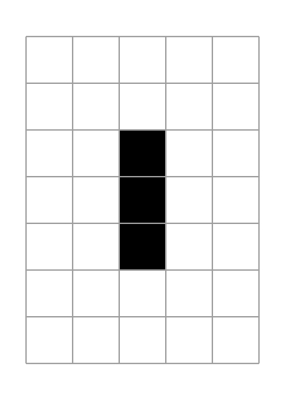
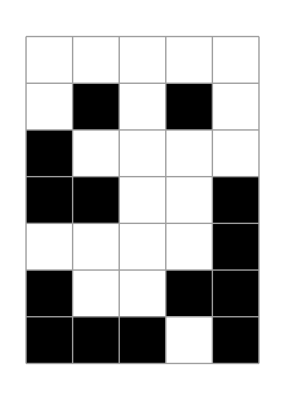
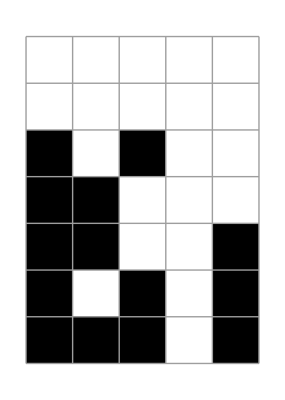
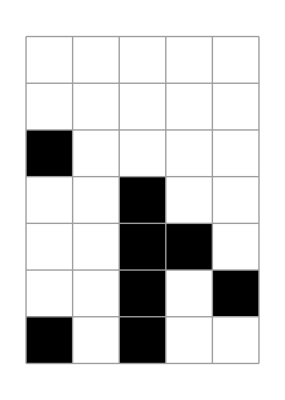
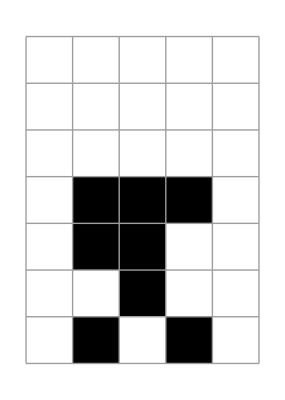
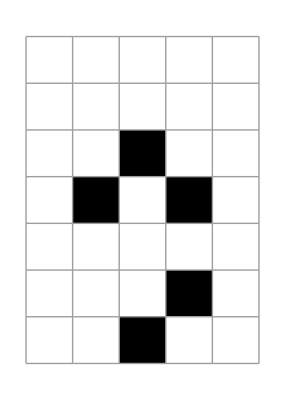
{0.390973,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}